```mathematica
number:=Table[If[x<10,"0"<>ToString[x],ToString[x]],{x,0,99}];classical =Table[File["C:\\Users\\oscar\\Documents\\ML\\EmelineOscarProjectMusic\\genres.tar\\genres\\genres\\classical\\classical.000"<>ToString[number⟦x⟧]<>".au"],{x,100}];
jazz =Table[File["C:\\Users\\oscar\\Documents\\ML\\EmelineOscarProjectMusic\\genres.tar\\genres\\genres\\jazz\\jazz.000"<>ToString[number⟦x⟧]<>".au"],{x,100}];
rock=Table[File["C:\\Users\\oscar\\Documents\\ML\\EmelineOscarProjectMusic\\genres.tar\\genres\\genres\\rock\\rock.000"<>ToString[number⟦x⟧]<>".au"],{x,100}];
hiphop=Table[File["C:\\Users\\oscar\\Documents\\ML\\EmelineOscarProjectMusic\\genres.tar\\genres\\genres\\hiphop\\hiphop.000"<>ToString[number⟦x⟧]<>".au"],{x,100}];
pop = Table[File["C:\\Users\\oscar\\Documents\\ML\\EmelineOscarProjectMusic\\genres.tar\\genres\\genres\\pop\\pop.000"<>ToString[number⟦x⟧]<>".au"],{x,100}];
popTest = Drop[pop,92];
pop = Drop[pop,-8];
classicalTest = Drop[classical,92];
classical = Drop[classical,-8];
rockTest = Drop[rock,92];
rock = Drop[rock,-8];
jazzTest = Drop[jazz,92];
jazz = Drop[jazz,-8];
hiphopTest = Drop[hiphop,92];
hiphop = Drop[hiphop,-8];
```

```mathematica
genres = {"classical","jazz","rock","hiphop","pop"};
musicGenres = Flatten[Table[Table[genres⟦x⟧,92],{x,5}]];
testGenres = Flatten[Table[Table[genres⟦x⟧,8],{x,5}]];
musicTest = Join[classicalTest,jazzTest,rockTest,hiphopTest,popTest];
```

```mathematica
data = Thread[Join[classical,jazz,rock,hiphop,pop]-> musicGenres];
validation = Thread[musicTest-> testGenres];
```

```mathematica
(*données pour tests*)
```

```mathematica
Clear[net];net=NetInitialize@NetChain[
{
ConvolutionLayer[64,12,"Interleaving"->True],
Ramp,
ConvolutionLayer[32,9,"Interleaving"->True],
Ramp,
AggregationLayer[Max,1],
LinearLayer[5],
SoftmaxLayer[]},
"Input"->NetEncoder[{"AudioMFCC","WindowSize"->640,"Offset"->320,"NumberOfFilters"-> 128,"NumberOfCoefficients"->128}],"Output"->NetDecoder[{"Class", genres}]];
```

```mathematica
trained = NetTrain[net,data,MaxTrainingRounds->18,"BatchSize"-> 4, TargetDevice->"GPU"]
```

NetChain[<>]

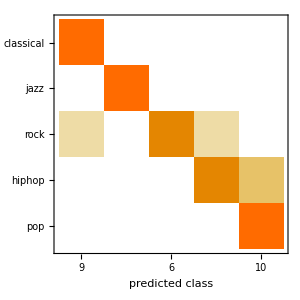
Classifier Measurements
Number of test examples | 40
Accuracy | 90. % ± 4.8 %
Accuracy baseline | 20. % ± 6.4 %
Geometric mean of probabilities | 0.419 ± 0.23
Mean cross entropy | 0.869 ± 0.53
Single evaluation time | 234. ms/example
Batch evaluation speed | 7.69 examples/s
Rejection rate | 0 %
-Graphics- |

```mathematica
measurements = ClassifierMeasurements[trained,validation,"Report"]
```

```mathematica
Clear[audio]
audio = AudioCapture[]
```

```mathematica
net2 = Import["C:\\Users\\oscar\\Documents\\ML\\EmelineOscarProjectMusic\\genres.tar\\CNN97,5.wlnet"]
```

NetChain[<>]

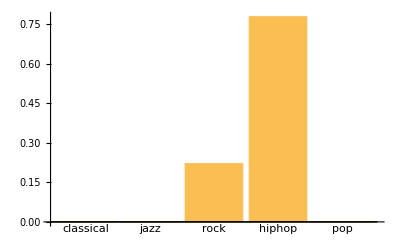

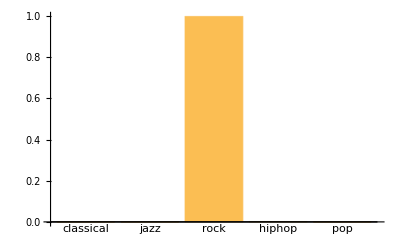

```mathematica
BarChart[trained[audio,"Probabilities"],ChartLabels-> genres]
BarChart[net2[audio,"Probabilities"],ChartLabels-> genres]
```

NetEncoder[<>]

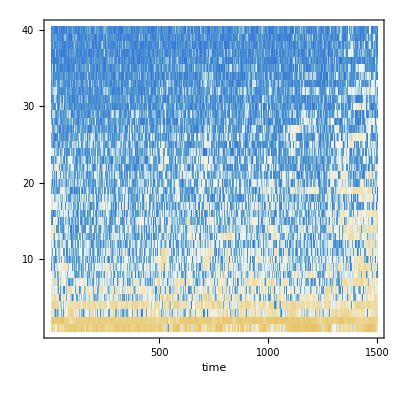

```mathematica
enc=NetEncoder[{"AudioMFCC","WindowSize"->320,"Offset"->320,"NumberOfCoefficients"->40}]
enc[rock[[1]]];
MatrixPlot[Log[Transpose[%]], { DataReversed -> {True, False},  FrameTicks -> {{True, False}, {True, False}},  FrameLabel -> {"", "time"}, AspectRatio -> 1}]
```

```mathematica
□_□
```

```mathematica
measurements = ClassifierMeasurements[trained,validation]
measurements["MisclassifiedExamples"]
```

ClassifierMeasurementsObject[…]

{File[C:\Users\oscar\Documents\ML\EmelineOscarProjectMusic\genres.tar\genres\genres\classical\classical.00092.au]→classical,File[C:\Users\oscar\Documents\ML\EmelineOscarProjectMusic\genres.tar\genres\genres\rock\rock.00099.au]→rock}

File[C:\Users\oscar\Documents\ML\EmelineOscarProjectMusic\genres.tar\genres\genres\jazz\jazz.00091.au]

```mathematica
measurements2 = ClassifierMeasurements[net2,validation]
```

ClassifierMeasurementsObject[…]

```mathematica
measurements2["MisclassifiedExamples"]
```

{File[C:\Users\oscar\Documents\ML\EmelineOscarProjectMusic\genres.tar\genres\genres\rock\rock.00099.au]→rock}